# Tichu Analyzer using Tichu-Logs from brettspielwelt.de

## Log Sources : tichulog.brettspielwelt.de

## Helper Functions

Initialize all Variables

```mathematica
Clear[arrLenght14,importTichuLogs,compareHands,countLoops]
```

```mathematica
countLoops = 0;
```

Checks if List is lower than 14 elements long

```mathematica
arrLenght14[a_List]:=If[Length[a]<14,{},a]
```

Checks how many of the cards of a specific hand are the same compered to all cards in the analysis

```mathematica
compareHands[hand_List,game_List,nLogs_]:=Module[{},
countLoops++;
If[Mod[countLoops,nLogs]==0,WriteString["stdout","."],""];
intersectionIncludingDuplicates[hand,#]&/@game
]
```

A special intersection function that takes duplicates into consideration

```mathematica
intersectionIncludingDuplicates[list1_List,list2_List]:=
ConstantArray[#,Min[Count[list1,#],Count[list2,#]]]&/@Intersection[list1,list2]//Flatten
```

## Main Functions

Imports the requested number of files and extracts the start hands that are included. It then removes the color information from all cards.

```mathematica
importTichuLogs[url_,type_]:=Module[{handsRaw,hands,rules},
handsRaw=DeleteCases[arrLenght14[#]&/@StringSplit[Cases[DeleteCases[StringCases[#,RegularExpression["(Dr\\s|Ph\\s){0,2}([SBRG](\\d+|[AKDB])\\s){10,14}(Ma\\s|Hu\\s){0,2}"]]&/@Import[url,"Lines"],{}],_?StringQ,∞]],{}];
rules = _~~#->#&/@Join[{"A","K","D","B","10"},Reverse[CharacterRange["1","9"]]];
If[type==1,StringReplace[#,rules]&/@handsRaw,handsRaw]
]
```

Iterates through all hands of the parameter list and analyses the number of same hands. The function returns a tuple with the raw data and the number of analyzed hands.

```mathematica
analyseGames[hands_List,nLogs_]:=Module[{g,nDupl,tmpHands,histVal},
tmpHands = Flatten[hands,1];
nDupl=compareHands[#,tmpHands,nLogs]&/@Flatten[hands,1];
histVal=Reverse[Sort[Length/@Flatten[nDupl,1]]];
{histVal,Length[tmpHands]}
]
```

## Start Function

Main Program function. It calls all the other functions and shows some status texts. If finally draws a histogram of the result.

```mathematica
start[nLogFiles_,type_]:=Module[{urls,histData},
{t1,b1}=AbsoluteTiming[
Print["Starting..."];
Print["Importing " <> ToString[nLogFiles] <> " log files..."];
urls =Take[Import["http://tichulog.brettspielwelt.de/","Hyperlinks"],-nLogFiles];
Print["Analyzing Data"];
histData=analyseGames[importTichuLogs[#,type]&/@urls,nLogFiles];
Print["Cleaning Data..."];
result=Drop[histData[[1]],histData[[2]]];
];
Print["Finished ("<>ToString[histData[[2]]]<>" hands with "<>ToString[Length[result]]<>" combinations analyzed)"];
Print["execution time: "<>ToString[t1]<>" Sekunden"];
Print["Standard Deviation: "<>ToString[N[StandardDeviation[result]]]];
Histogram[result,LabelingFunction->Above,Ticks-> Automatic,ImageSize->Large]
]
```

## Start Analysis here...

Call the start function with the desired number of log files to analyse (max. about 600) and the type of analyses.
start[n,t]:	the n latest log files which are linked on tichulog.brettspielwelt.de with comparison type  (1) “relaxed  data” or (2) “precise data”.
relaxed data = only compare the value but not the color of the cards (i.E. a red 4 is treated the same as a blue 4).
precise data = compare the exact cards (a blue king ist not the same like a green king)
Exsamples:
start[20,1]: analyse the latest 20 log files that are linked in the overview page with comparison type  “relaxed data”
start[50,2]: analyse the latest 50 log files with comparison type “precise data”

Starting...

Importing 10 log files...

Analyzing Data

....................................

Cleaning Data...

Finished (352 hands with 123552 combinations analyzed)

execution time: 3.85054 Sekunden

Standard Deviation: 1.48268

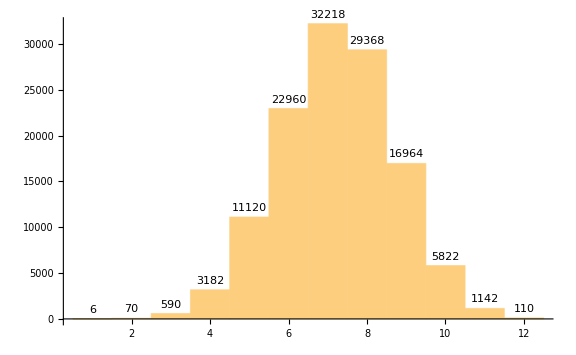

```mathematica
start[10,1]
```